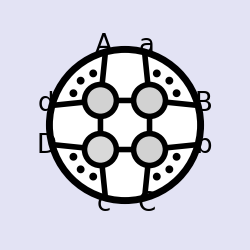
-Graphics-
One-Loop Amplitude Integrands
and Integrals in N=4 SYM
Jacob L. Bourjaily, 2013

```mathematica
SetDirectory[NotebookDirectory[]];
<<abcode.wl
<<loop_amplitudes.m
```

```mathematica
(*a<b*)
```

```mathematica
boxCoeff[{Z1_,Z2_},{a_Integer,b_Integer}]:=Block[{out,lista=Delete[X/@Range[6],a],listb=Delete[X/@Range[6],b]},
dot[i_,i_]:=0;
P=Delete[Range[6],{{a},{b}}];
normal=-X[p,r]X[q,s]Sqrt[(1-(X[p,q]X[r,s])/(X[p,r]X[q,s])-(X[q,r]X[p,s])/(X[p,r]X[q,s]))^2-4(X[p,q]X[r,s])/(X[p,r]X[q,s])(X[q,r]X[p,s])/(X[p,r]X[q,s])]/.X[i_,j_]:>dot[X[i],X[j]]/.p:>P[[1]]/.q:>P[[2]]/.r:>P[[3]]/.s:>P[[4]];
out=((Det[Table[dot[i,j],{i,Flatten[{X/@Range[a-1],Z1,X/@Range[a+1,6]}]},{j,X/@Range[6]}]]/Det[Table[dot[X[i],X[j]],{i,6},{j,6}]])(Det[Table[dot[i,j],{i,Flatten[{lista[[1;;b-2]],Z2,lista[[b;;]]}]},{j,lista}]]/Det[Table[dot[i,j],{i,lista},{j,lista}]]))+((Det[Table[dot[i,j],{i,Flatten[{X/@Range[b-1],Z1,X/@Range[b+1,6]}]},{j,X/@Range[6]}]]/Det[Table[dot[X[i],X[j]],{i,6},{j,6}]])Det[Table[dot[i,j],{i,listb/.X[a]:>Z2},{j,listb}]]/Det[Table[dot[i,j],{i,listb},{j,listb}]]);
Clear[dot];
	(40)out/normal
];
```

```mathematica
Table[boxCoeff[{Z1,Z2},{i,j}]/.X[i_]:>Mod[{i,i+1},6,1]/.{Z1:>{1,3},Z2:>{4,6}}/.dot[x___]:>ab@@Flatten[{x}]//neab1,{j,2,6},{i,1,j-1}]//Flatten
```

{1,-1,0,1,0,0,0,1,-1,1,0,-1,1,-1,0}

```mathematica
(Table[box[Complement[Range[6],{i,j}]],{j,2,6},{i,1,j-1}]//Flatten)
```

{box[{3,4,5,6}],box[{2,4,5,6}],box[{1,4,5,6}],box[{2,3,5,6}],box[{1,3,5,6}],box[{1,2,5,6}],box[{2,3,4,6}],box[{1,3,4,6}],box[{1,2,4,6}],box[{1,2,3,6}],box[{2,3,4,5}],box[{1,3,4,5}],box[{1,2,4,5}],box[{1,2,3,5}],box[{1,2,3,4}]}

```mathematica
P=Delete[Range[6],{{5},{6}}];(*a<b*)
normal=-X[p,r]X[q,s]Sqrt[(1-(X[p,q]X[r,s])/(X[p,r]X[q,s])-(X[q,r]X[p,s])/(X[p,r]X[q,s]))^2-4(X[p,q]X[r,s])/(X[p,r]X[q,s])(X[q,r]X[p,s])/(X[p,r]X[q,s])]/.X[i_,j_]:>dot[X[i],X[j]]/.p:>P[[1]]/.q:>P[[2]]/.r:>P[[3]]/.s:>P[[4]]/.X[i_]:>Mod[{i,i+1},6,1]/.dot[x___]:>ab@@Flatten[{x}]//neab1
```

-1

-1

-1

{5/2,-90,0,160,0,0,0,160,-90,5/2,0,-9/10,32/5,-9/10,0}

```mathematica
Position[%27,0]//Flatten
```

```mathematica
(*Normalization factor can be found from 1303.4734*)
P=Delete[Range[6],{{1},{2}}]
```

{3,4,5,6}

```mathematica
normal=-X[a,c]X[b,d]Sqrt[(1-(X[a,b]X[c,d])/(X[a,c]X[b,d])-(X[b,c]X[a,d])/(X[a,c]X[b,d]))^2-4(X[a,b]X[c,d])/(X[a,c]X[b,d])(X[b,c]X[a,d])/(X[a,c]X[b,d])]/.X[i_,j_]:>dot[X[i],X[j]]/.p:>P[[1]]/.q:>P[[2]]/.r:>P[[3]]/.s:>P[[4]]/.X[i_]:>Mod[{i,i+1},6,1]/.dot[x___]:>ab@@Flatten[{x}];
```

```mathematica
normalisation
normal
```

-ab[1,2,3,4] ab[2,3,4,5]

√(ab[3,4,5,6]^2 ab[4,5,6,1]^2)

```mathematica
P=Delete[Range[6],{{1},{2}}];
norm1=ab[P[[1]],P[[1]]+1,P[[3]],P[[3]]+1];
norm2=ab[P[[2]],P[[2]]+1,P[[4]],P[[4]]+1];
u=(ab[P[[1]],P[[1]]+1,P[[2]],P[[2]]+1]ab[P[[3]],P[[3]]+1,P[[4]],P[[4]]+1])/(ab[P[[1]],P[[1]]+1,P[[3]],P[[3]]+1]ab[P[[2]],P[[2]]+1,P[[4]],P[[4]]+1]);
v=(ab[P[[2]],P[[2]]+1,P[[3]],P[[3]]+1]ab[P[[1]],P[[1]]+1,P[[4]],P[[4]]+1])/(ab[P[[1]],P[[1]]+1,P[[3]],P[[3]]+1]ab[P[[2]],P[[2]]+1,P[[4]],P[[4]]+1]);
delta=Sqrt[(1-u-v)^2-4(u)(v)];
norma1=ab[P[[1]],P[[1]]+1,P[[3]],P[[3]]+1];
norma2=ab[P[[2]],P[[2]]+1,P[[4]],1];
uspec=(ab[P[[1]],P[[1]]+1,P[[2]],P[[2]]+1]ab[P[[3]],P[[3]]+1,P[[4]],1])/(ab[P[[1]],P[[1]]+1,P[[3]],P[[3]]+1]ab[P[[2]],P[[2]]+1,P[[4]],1]);
vspec=(ab[P[[2]],P[[2]]+1,P[[3]],P[[3]]+1]ab[P[[1]],P[[1]]+1,P[[4]],1])/(ab[P[[1]],P[[1]]+1,P[[3]],P[[3]]+1]ab[P[[2]],P[[2]]+1,P[[4]],1]);
deltaspec=Sqrt[(1-uspec-vspec)^2-4(uspec)(vspec)(deltaspec)];
      If[b!=6,normalisation=-(norma1)(norma2),normalisation=-(norm1)(norm2)(deltaspec)];
```

```mathematica
normalisation
```

```mathematica
normalas=Sqrt[((dot[X[P[[1]]],X[P[[3]]]])(dot[X[P[[2]]],X[P[[4]]]])-(dot[X[P[[1]]],X[P[[2]]]])(dot[X[P[[3]]],X[P[[4]]]])-(dot[X[P[[2]]],X[P[[3]]]])(dot[X[P[[1]]],X[P[[4]]]]))^2-4(dot[X[P[[1]]],X[P[[2]]]])(dot[X[P[[3]]],X[P[[4]]]])(dot[X[P[[2]]],X[P[[3]]]])(dot[X[P[[1]]],X[P[[4]]]])]/.X[i_]:>Mod[{i,i+1},6,1]/.dot[x___]:>ab@@Flatten[{x}]
```

```mathematica
P=Delete[Range[6],{{1},{2}}]
```

```mathematica
normalas=Sqrt[((dot[X[P[[1]]],X[P[[3]]]])(dot[X[P[[2]]],X[P[[4]]]])-(dot[X[P[[1]]],X[P[[2]]]])(dot[X[P[[3]]],X[P[[4]]]])-(dot[X[P[[2]]],X[P[[3]]]])(dot[X[P[[1]]],X[P[[4]]]]))^2-4(dot[X[P[[1]]],X[P[[2]]]])(dot[X[P[[3]]],X[P[[4]]]])(dot[X[P[[2]]],X[P[[3]]]])(dot[X[P[[1]]],X[P[[4]]]])]/.X[i_]:>Mod[{i,i+1},6,1]/.X[i_]:>Mod[{i,i+1},6,1]/.dot[x___]:>ab@@Flatten[{x}]
```

```mathematica
P=Delete[Range[6],{{1},{2}}];
normalas=Sqrt[((dot[X[i],X[k]])(dot[X[j],X[l]])-(dot[X[i],X[j]])(dot[X[k],X[l]])-(dot[X[j],X[k]])(dot[X[i],X[l]]))^2-4(dot[X[i],X[j]])(dot[X[k],X[l]])(dot[X[j],X[k]])(dot[X[i],X[l]])]/.i:>P[[1]]/.j:>P[[2]]/.k:>P[[3]]/.l:>P[[4]]/.X[i_]:>Mod[{i,i+1},6,1]/.dot[x___]:>ab@@Flatten[{x}]
```

```mathematica
P=Delete[Range[6],{{3},{6}}]
```

```mathematica
normalas=Sqrt[((dot[X[p],X[r]])(dot[X[q],X[s]])-(dot[X[p],X[q]])(dot[X[r],X[s]])-(dot[X[q],X[r]])(dot[X[p],X[s]]))^2-4(dot[X[p],X[q]])(dot[X[r],X[s]])(dot[X[q],X[r]])(dot[X[p],X[s]])]/.p:>P[[1]]/.q:>P[[2]]/.r:>P[[3]]/.s:>P[[4]]/.X[i_]:>Mod[{i,i+1},6,1]/.dot[x___]:>ab@@Flatten[{x}]//neab1
```

```mathematica
normal1=ab[6,P[[1]],P[[3]]-1,P[[3]]]
Deltanorma=Sqrt[(1-(ab[6,P[[1]],P[[2]]-1,P[[2]]]ab[P[[3]]-1,P[[3]],P[[4]]-1,P[[4]]])/(ab[6,P[[1]],P[[3]]-1,P[[3]]]ab[P[[2]]-1,P[[2]],P[[4]]-1,P[[4]]])-(ab[P[[2]]-1,P[[2]],P[[3]]-1,P[[3]]]ab[6,P[[1]],P[[4]]-1,P[[4]]])/(ab[6,P[[1]],P[[3]]-1,P[[3]]]ab[P[[2]]-1,P[[2]],P[[4]]-1,P[[4]]]))^2-4(ab[6,P[[1]],P[[2]]-1,P[[2]]]ab[P[[3]]-1,P[[3]],P[[4]]-1,P[[4]]])/(ab[6,P[[1]],P[[3]]-1,P[[3]]]ab[P[[2]]-1,P[[2]],P[[4]]-1,P[[4]]])(ab[P[[2]]-1,P[[2]],P[[3]]-1,P[[3]]]ab[6,P[[1]],P[[4]]-1,P[[4]]])/(ab[6,P[[1]],P[[3]]-1,P[[3]]]ab[P[[2]]-1,P[[2]],P[[4]]-1,P[[4]]])]
```

```mathematica
If[a!=1,normalisation=(normal1)(norm2)(Deltanorma),(norm1)(norm2)(Delta)];
```

```mathematica
P=Delete[Range[6],{{a},{b}}]
```

```mathematica
ab[P[[1]]-1,P[[1]],P[[3]]-1,P[[3]]]
```

```mathematica
normalisation=-ab[P[[1]]-1,P[[1]],P[[3]]-1,P[[3]]]ab[P[[2]]-1,P[[2]],P[[4]]-1,P[[4]]]Delta//neab1
```

```mathematica
Delta
```

```mathematica
normal1=ab[6,P[[1]],P[[3]]-1,P[[3]]]
Deltanorma=Sqrt[(1-(ab[6,P[[1]],P[[2]]-1,P[[2]]]ab[P[[3]]-1,P[[3]],P[[4]]-1,P[[4]]])/(ab[6,P[[1]],P[[3]]-1,P[[3]]]ab[P[[2]]-1,P[[2]],P[[4]]-1,P[[4]]])-(ab[P[[2]]-1,P[[2]],P[[3]]-1,P[[3]]]ab[6,P[[1]],P[[4]]-1,P[[4]]])/(ab[6,P[[1]],P[[3]]-1,P[[3]]]ab[P[[2]]-1,P[[2]],P[[4]]-1,P[[4]]]))^2-4(ab[6,P[[1]],P[[2]]-1,P[[2]]]ab[P[[3]]-1,P[[3]],P[[4]]-1,P[[4]]])/(ab[6,P[[1]],P[[3]]-1,P[[3]]]ab[P[[2]]-1,P[[2]],P[[4]]-1,P[[4]]])(ab[P[[2]]-1,P[[2]],P[[3]]-1,P[[3]]]ab[6,P[[1]],P[[4]]-1,P[[4]]])/(ab[6,P[[1]],P[[3]]-1,P[[3]]]ab[P[[2]]-1,P[[2]],P[[4]]-1,P[[4]]])]
normalisation//neab1
```

```mathematica
(X[p,r]X[q,s]-X[p,q]X[r,s]-X[q,r]X[p,s])^2-4X[p,q]X[r,s]X[q,r]X[p,s]/.X[i_,j_]:>dot[X[i],X[j]]
```